## Math 137 Sp 19 Mathematica Hw 3 Integration, Volumes and Arclength. Ernst

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the homework turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work.

Due: Friday, March 15

#### An example of problem 1

```mathematica
∫ⅇ^(x^2)ⅆx
```

1/2 √π Erfi[x]

```mathematica
?Erfi
```

Erfi[z] gives the imaginary error function erf(iz)/i.

Form the documentation center

The imaginary error function is given by erfi(z)==erf(iz)/i and erf(z)==2/√π∫_0^z e^(-t^2)dt

At http://www.mathworks.com/help/symbolic/mupad_ref/erfi.html

erfi(x)=2/(√π)∫_0^x ⅇ^(t^2)ⅆt    computes the imaginary error function.

#### ArcLength - a more general formula using parametric plots

Here's a strange region R plotted in the xy-plane.

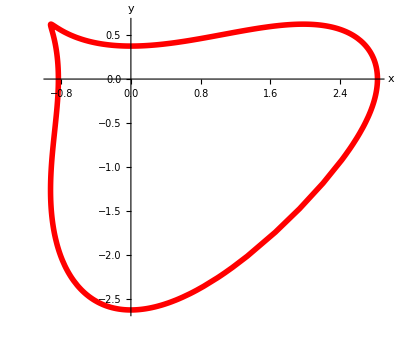

```mathematica
Clear[x,y,t]
x[t_]:=Cos[t] (2+Cos[t]-1/6 Cos[2 t])

y[t_]:=Sin[t] (1.5-Sin[t]+1/8 Sin[3 t])

Rplot=ParametricPlot[{x[t],y[t]},{t,0,2 π},
		PlotRange->All,PlotStyle->{{Red,Thickness[0.01]}},AxesLabel->{"x","y"}]
```

Its arc-length can be compute by

```mathematica
∫_0^(2π) √((x'[t])^2+(y'[t])^2)ⅆt
```

$Aborted

No go with that, so we try it numerically.

```mathematica
NIntegrate[√((x'[t])^2+(y'[t])^2),{t,0,2π}]
```

11.973

Now we move this curve into 3 dimensions.

```mathematica
Clear[x,y,z,t]
x[t_]:=Cos[t] (2+Cos[t]-1/6 Cos[2 t])

y[t_]:=Sin[t] (1.5-Sin[t]+1/8 Sin[3 t])

z[t_]:=Sin[3t]

Rplot=ParametricPlot3D[{x[t],y[t],z[t]},{t,0,2 π},
		PlotRange->All,PlotStyle->{{Red,Thickness[0.01]}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Its arc-length can be compute by

```mathematica
∫_0^(2π) √((x'[t])^2+(y'[t])^2+(z'[t])^2)ⅆt
```

$Aborted

No go with that, so we try it numerically.

```mathematica
NIntegrate[√((x'[t])^2+(y'[t])^2+(z'[t])^2),{t,0,2π}]
```

17.8233

### Homework

#### Problem 1 Integration yields special functions

We all know that integration is “difficult”. Mathematica uses a number of tricks to still give answers to difficult functions. In this exercise we test Mathematica’s integration skills.

(i) Find five different functions y=f(x) where Mathematica returns the integral ∫f(x)ⅆx unchanged. Not different means that you should not use the same function and make simple changes such as multiply it by a constant or add a “trivial term to it”.

(ii) Find five different functions y=f(x) where Mathematica returns the integral ∫f(x)ⅆx by using a “special function”, which is defined as an integral. Here the five functions should have answers involving five different special functions. 

For each function 
Find the definition of the function (as an integral). 
(You can do this by looking at the documentation center. This may take some time to find it so you can also google this if you like.)

#### Problem I1 Knotted curves

Given a two parameter family of knotted curves in three space. Assume that p and q are positive integers with p>q≥2 and gcd(p,q)=1.

x(t) =cos(q t)(3+cos(p t)
y(t) =sin(q t)(3+cos(p t)
z(t) =sin(p t)

Here is an example of such a curve for p=3 and q=2.

```mathematica
ParametricPlot3D[{x[t,3,2],y[t,3,2],z[t,3,2]},{t,0,2 π},
		PlotRange->All,PlotStyle->{Thickness[0.03]},ColorFunction->"DarkRainbow",AxesLabel->{"x","y","z"}]
```

-Graphics3D-

(i) Compute the arc-length of these curves or all pairs (see the above restrictions) with 3≤p≤8.
(ii) Look at the plots of the examples generated by (i) and see if you can figure out how to describe the curves using the parameters p and q.

#### Problem I1I Volume measurements for tubes and horns

Here is a modest curve shown with the three coordinate axes in three dimensions:

```mathematica
h=5;
spacer=h/10;
threedims=Graphics3D[{{Blue,Line[{{-h,0,0},{h,0,0}}]},Text["x",{h+spacer,0,0}],{Blue,Line[{{0,-h,0},{0,h+1,0}}]},Text["y",{0,h+1+spacer,0}],{Blue,Line[{{0,0,-h/2},{0,0,h+2}}]},Text["z",{0,0,h+2+spacer}]}];
Clear[t,curveplotter];
curveplotter[t_]:={Cos[t],3 t Sin[t],3 t}

curve=ParametricPlot3D[curveplotter[t],{t,0,2}];

Show[threedims,curve,Boxed->False,PlotRange->All]
```

Here is the same curve shown with a few sample circles parallel to the xy-plane and centered on the curve:

```mathematica
Clear[t];
circle1=ParametricPlot3D[Evaluate[curveplotter[0.5]+2 {Cos[t],Sin[t],0}],{t,0,2 π}];

circle2=ParametricPlot3D[Evaluate[curveplotter[1]+2 {Cos[t],Sin[t],0}],{t,0,2 π}];

circle3=ParametricPlot3D[Evaluate[curveplotter[1.5]+2 {Cos[t],Sin[t],0}],{t,0,2 π}];

Show[threedims,curve,circle1,circle2,circle3,Boxed->False,PlotRange->All]
```

Here's what you get when you make a tube consisting of all such circles:

```mathematica
Clear[tubeplotter,s,t];
tubeplotter[s_,t_]:=curveplotter[t]+2 {Cos[s],Sin[s],0}

tube=ParametricPlot3D[Evaluate[tubeplotter[s,t]],{t,0,2},{s,0,2 π}];

tubeplot=Show[threedims,tube,curve,Boxed->False,PlotRange->All]
```

Move each circle in its own plane but so that it is centered on the z-axis:

```mathematica
Clear[cylinderplotter,s,t];
cylinderplotter[s_,t_]:={0,0,curveplotter[t]⟦3⟧}+2 {Cos[s],Sin[s],0}
```

Compare:

```mathematica
tubeplotter[s,t]
```

{2 Cos[s]+Cos[t],2 Sin[s]+3 t Sin[t],3 t}

```mathematica
Clear[s,t];
cylinder=ParametricPlot3D[cylinderplotter[s,t],{t,0,2},{s,0,2 π},Boxed->False]
```

Here it is all combined:

```mathematica
Show[cylinder,threedims,tube,Boxed->False,PlotRange->All]
```

(i) The cylinder has a base with radius 2, and the height of the cylinder is 6=3(2), so the volume of the cylinder measures out to
       2^2 π (6)=24π cubic units. 
Explain why the volume of the tube also measures out to 24π cubic units.

(ii) If you go back to the beginning, keeping everything the same but changing 
       curveplotter[t]={Cos[t],3tSin[t],3t} 
to
       curveplotter[t]={f[t],g[t],3t}
where f[t] and g[t] are any functions you care to use, then how do you know that the volume of the resulting tube measures out to 12π cubic units? Explain and produce a new tube plot for a new set of functions f(t)  and g(t)

(iii) Look at this plot:

```mathematica
h=5;
spacer=h/10;
threedims=Graphics3D[{{Blue,Line[{{-h,0,0},{h,0,0}}]},Text["x",{h+spacer,0,0}],{Blue,Line[{{0,-h,0},{0,h+1,0}}]},Text["y",{0,h+1+spacer,0}],{Blue,Line[{{0,0,-h/2},{0,0,h+2}}]},Text["z",{0,0,h+2+spacer}]}];

CMView={2.7,1.6,1.2};
Clear[s,t,curveplotter,hornplotter,radius];

curveplotter[t_]:={t (4-t),t,t^2/4};

radius[t_]=0.75 t;

hornplotter[s_,t_]=curveplotter[t]+radius[t] {Cos[s],0,Sin[s]};

horn=ParametricPlot3D[hornplotter[s,t],{t,0,4},{s,0,2 π}];

hornplot=Show[threedims,horn,Boxed->False,PlotRange->All]
```

The cross sections of this horn sliced by planes parallel to the xz-plane are circles of varying radiuses. Move each circle in its own plane but so that it is centered on the y-axis; and use what you see to measure the volume of this horn.

(iv) Start with a base curve specified by
       curveplotter[t]={t,f[t],g[t]} 
with a≤t≤b. 
Build a horn by centering at each point {t,f[t],g[t]} a circle of radius r[t] parallel to the yz plane.
Write down a formula that everyone can use to measure the volume of this horn.